```mathematica
AppendTo[$Path, NotebookDirectory[]];
```

```mathematica
Get["CubeAcquire.wl"]
Get["CubeVisualize.wl"]
Get["CubeCore.wl"]
```

```mathematica
cubeString = sampleStrings["solved"]
```

WWWWWWWWWOOOGGGRRRBBBOOOGGGRRRBBBOOOGGGRRRBBBYYYYYYYYY

## 2D Cube

```mathematica
cube2D = Generate2DCube[cubeString];
```

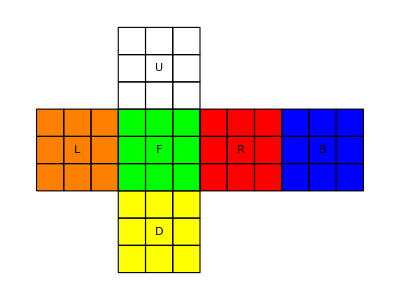

```mathematica
Visualize2DCube[cube2D];
```

## 3D Cube

```mathematica
cube3DPieces = GetPieces[cubeString];
```

```mathematica
cube3D = Dynamic[Generate3DCube[cube3DPieces]];
```

```mathematica
Visualize3DCube[cube3D];
```

-Graphics3D-

### Controlli

#### Generale

```mathematica
List[
Button["Load solved",cube3DPieces=GetPieces[sampleStrings["solved"]];],
Button["Load start",cube3DPieces=GetPieces[sampleStrings["start"]];]
]
```

{Load solved,Load start}

#### Mosse standard cubo

```mathematica
List[Button["L",cube3DPieces=RotateL[cube3DPieces];],Button["L'",cube3DPieces=RotateLi[cube3DPieces];],Button["R",cube3DPieces=RotateR[cube3DPieces];],Button["R'",cube3DPieces=RotateRi[cube3DPieces];],Button["U",cube3DPieces=RotateU[cube3DPieces];],Button["U'",cube3DPieces=RotateUi[cube3DPieces];],Button["D",cube3DPieces=RotateD[cube3DPieces];],Button["D'",cube3DPieces=RotateDi[cube3DPieces];],Button["F",cube3DPieces=RotateF[cube3DPieces];],Button["F'",cube3DPieces=RotateFi[cube3DPieces];],Button["B",cube3DPieces=RotateB[cube3DPieces];],Button["B'",cube3DPieces=RotateBi[cube3DPieces];]]
```

{L,L',R,R',U,U',D,D',F,F',B,B'}

#### Rotazione cubo

```mathematica
List[Button["X",cube3DPieces=RotateX[cube3DPieces];],Button["X'",cube3DPieces=RotateXi[cube3DPieces];],Button["Y",cube3DPieces=RotateY[cube3DPieces];],Button["Y'",cube3DPieces=RotateYi[cube3DPieces];],Button["Z",cube3DPieces=RotateZ[cube3DPieces];],Button["Z'",cube3DPieces=RotateZi[cube3DPieces];]]
```

{X,X',Y,Y',Z,Z'}

```mathematica
(*Restituisce un cubo nell'insieme totale,a partire dall'elemento*)
getCube[total_,element_]:=(First[Position[total,element]]);

(*Restituisce gli indici dei cubi nell'insieme totale a partire da un pattern in un certo set di elementi riguardante la posizione*)
getPos[total_,elements_,pattern_]:=(idxs=Flatten[Position[Table[Flatten[Cases[{elements[[t]]["pos"]},pattern]],{t,1,Length[elements]}],pattern]];
Return[Flatten[Table[getCube[total,elements[[idxs[[t]]]]],{t,1,Length[idxs]}]]]);

(*Restituisce gli indici dei cubi nell'insieme totale a partire da un pattern in un certo set di elementi riguardante i colori*)
getCol[total_,elements_,pattern_]:=(idxs=Flatten[Position[Table[Flatten[Cases[{elements[[t]]["colors"]},pattern]],{t,1,Length[elements]}],pattern]];
Return[Flatten[Table[getCube[total,elements[[idxs[[t]]]]],{t,1,Length[idxs]}]]]);

(* Restituisce l'indice di un cubo che soddisfa un certo pattern di colori permutati *)
getColSort[total_, elements_,col1_, col2_, col3_] := (Flatten[{
getCol[cube3DPieces,cube3DPieces,{col1,col2, col3}],getCol[cube3DPieces,cube3DPieces,{col1,col3, col2}],getCol[cube3DPieces,cube3DPieces,{col2,col1, col3}],
getCol[cube3DPieces,cube3DPieces,{col3,col1, col2}],getCol[cube3DPieces,cube3DPieces,{col3,col2, col1}],getCol[cube3DPieces,cube3DPieces,{col2,col3, col1}]}])

(*Inserisce un white edge al second floor nella faccia superiore*)
setSFDaisy[SFWhiteEdge_]:=(checkW=SFWhiteEdge["colors"][[1]]=="W"; Switch[SFWhiteEdge["pos"],
{1,0,1},(If[checkW,cube3DPieces=RotateFi[cube3DPieces],cube3DPieces=RotateR[cube3DPieces]]),
{1,0,-1},(If[checkW,cube3DPieces=RotateB[cube3DPieces],cube3DPieces=RotateRi[cube3DPieces]]),
{-1,0,1},(If[checkW,cube3DPieces=RotateF[cube3DPieces],cube3DPieces=RotateLi[cube3DPieces]]),
{-1,0,-1},(If[checkW,cube3DPieces=RotateBi[cube3DPieces],cube3DPieces=RotateL[cube3DPieces]])])
```

```mathematica
(*Specifica dei numeri di facce none per ogni cubo nell'insieme cube3DPieces,per riconoscere corner,edges e centers*)numberOfNone:=Table[Count[cube3DPieces[[t]]["colors"],None],{t,1,Length[cube3DPieces]}];

(*Ricerca degli edges bianchi*)
idxOfEdges:=Flatten[Position[numberOfNone,1]];
idxWhiteEdges:=getCol[cube3DPieces,cube3DPieces[[idxOfEdges]],{___,"W",___}];
whiteEdges:=cube3DPieces[[idxWhiteEdges]]

(*Ricerca dei petali che devono diventare bianchi*)
idxPetali:=Flatten[{Flatten[getPos[cube3DPieces,cube3DPieces,{1|-1,1,0}]],Flatten[getPos[cube3DPieces,cube3DPieces,{0,1,1|-1}]]}];
petali := cube3DPieces[[idxPetali]]
(* Specifica dei petali che hanno già una faccia superiore bianca *)
rightPetali := cube3DPieces[[getCol[cube3DPieces,petali,{_,"W",_}]]]
```

```mathematica
(* Controlla il cubo nella faccia superiore rispetto ad una faccia bianca (si può dire o è razzista?)*)
getWTop[element_] := Switch[element["pos"][[2]],
1,  element, (*devo trasformarlo in un 2F ma il top è lui *)
0, If[ MatchQ[element["colors"],{_,_,"W"}], (* Faccia bianca o su Front-Back o su Left-Right *)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,0}]]]] ,(*FB mantengo X*)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{0,1,element["pos"][[3]]}]]] ](*LR mantengo Z*)
],
-1, If[MatchQ[element["colors"],{_,"W",_}], (* Faccia bianca o su Up-Down o su Front-Back *)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,element["pos"][[3]]}]]] ], (*UD mantengo Z e X*)
First[cube3DPieces[[ getPos[cube3DPieces,cube3DPieces,{element["pos"][[1]],1,element["pos"][[3]]}]]]]  (*FB devo trasformarlo in un 2F prima, quindi controllo solo quella sopra, ma andrà fatto un doppio controllo*)
]
]

(* Da chiamare dopo aver fatto i giusti check con getWTop, rende un edge con una faccia bianca un edge da 2o piano *)
makeSF[element_] := 
(While[getWTop[element]["colors"][[2]] == "W", cube3DPieces = RotateU[cube3DPieces]];
Switch[element["pos"][[1]],
   0, If[element["pos"][[3]] == -1, cube3DPieces = RotateB[cube3DPieces], cube3DPieces = RotateF[cube3DPieces]], (* Se dietro, B, se davanti, F*)
   1, cube3DPieces = RotateR[cube3DPieces], (* se a dx, R *)
-1, cube3DPieces = RotateL[cube3DPieces] (* se a sx, L *)
];
)

(* Gli edges da inserire sono quelli che non fanno ancora parte dei petali al posto giusto *)
leftEdges := Complement[whiteEdges, rightPetali]
```

```mathematica
(* ADESSO PARLO IO [ALGORITMO EPICO FINITO MALE]
	Finché ci sono dei leftEdges, mi salvo i colori del cubetto che sto considerando così gli assegno un cubetto senza che cambi in continuazione. Poi, finché questo cubetto
	non fa parte dei rightPetali, lo rendo un second floor, libero il cubo in alto da una faccia bianca facendo quante UP servono e faccio la mossa giusta per portarlo in alto
	con setSFDaisy
*)

While[Length[leftEdges] != 0,
 {col1,col2,col3}= First[cube3DPieces[[getCube[cube3DPieces,First[leftEdges]]]]]["colors"];
 edge:= First[cube3DPieces[[getColSort[cube3DPieces,cube3DPieces,col1,col2,col3]]]];
While[Intersection[List[edge],rightPetali] == {},
If[edge["pos"][[2]] != 0,makeSF[edge]];
While[getWTop[edge]["colors"][[2]] == "W", cube3DPieces = RotateU[cube3DPieces]];
setSFDaisy[edge];
];
]

idxCenters = Flatten[Position[numberOfNone,2]];
centers = cube3DPieces[[idxCenters]];
lateralCenters = Complement[centers ,cube3DPieces[[getColSort[cube3DPieces,centers,None,None,"W"|"Y"]]]]
```

{<|pos→{-1,0,0},colors→{O,None,None}|>,<|pos→{0,0,-1},colors→{None,None,G}|>,<|pos→{0,0,1},colors→{None,None,B}|>,<|pos→{1,0,0},colors→{R,None,None}|>}

```mathematica
While[Length[rightPetali]!= 0,
{col1,col2,col3}= First[cube3DPieces[[getCube[cube3DPieces,First[rightPetali]]]]]["colors"];
edge :=  First[cube3DPieces[[getColSort[cube3DPieces,cube3DPieces,col1,col2,col3]]]];

]
```

```mathematica
rightPetali
cube3DPieces
```

{<|pos→{-1,1,0},colors→{R,W,None}|>,<|pos→{1,1,0},colors→{G,W,None}|>,<|pos→{0,1,1},colors→{None,W,B}|>,<|pos→{0,1,-1},colors→{None,W,O}|>}

{<|pos→{1,0,0},colors→{R,None,None}|>,<|pos→{-1,0,0},colors→{O,None,None}|>,<|pos→{0,1,0},colors→{None,Y,None}|>,<|pos→{0,-1,0},colors→{None,W,None}|>,<|pos→{0,0,1},colors→{None,None,B}|>,<|pos→{0,0,-1},colors→{None,None,G}|>,<|pos→{-1,1,0},colors→{R,W,None}|>,<|pos→{0,1,1},colors→{None,W,B}|>,<|pos→{1,1,0},colors→{G,W,None}|>,<|pos→{0,-1,-1},colors→{None,B,Y}|>,<|pos→{-1,0,-1},colors→{B,None,O}|>,<|pos→{-1,-1,0},colors→{G,O,None}|>,<|pos→{-1,0,1},colors→{R,None,G}|>,<|pos→{1,0,1},colors→{R,None,B}|>,<|pos→{1,0,-1},colors→{R,None,Y}|>,<|pos→{1,-1,0},colors→{O,Y,None}|>,<|pos→{0,-1,1},colors→{None,G,Y}|>,<|pos→{0,1,-1},colors→{None,W,O}|>,<|pos→{1,1,1},colors→{W,O,G}|>,<|pos→{1,-1,1},colors→{W,B,R}|>,<|pos→{-1,-1,-1},colors→{W,R,G}|>,<|pos→{-1,1,1},colors→{B,Y,R}|>,<|pos→{1,1,-1},colors→{O,Y,B}|>,<|pos→{1,-1,-1},colors→{B,O,W}|>,<|pos→{-1,-1,1},colors→{G,Y,R}|>,<|pos→{-1,1,-1},colors→{G,O,Y}|>}